```mathematica
(*SuperradiantLaser, cumulant;
  using bash;
  Variables v.s. repumping w*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*Parameters*)
nMax=200;
init=.1;
interval=.1;
nAtom = 100;
(*Get data*)
(*Set up bins*)
intensity=Table[0,{i,nMax}];
intensityUnCor=Table[0,{i,nMax}];
inversion =Table[0,{i,nMax}];
spinSpinCor=Table[0,{i,nMax}];
w=Table[0,{i,nMax}];
(*Input values*)
For[i=0,i<nMax,i++,
w[[i+1]] =init+interval i;
wForm= NumberForm[w[[i+1]],{10,1}];
intensityData=Flatten[Import[NotebookDirectory[]<>"N"<>ToString[nAtom]<>"_repumping"<>ToString[wForm]<>"/intensity.dat"]];
intensityUnCorData=Flatten[Import[NotebookDirectory[]<>"N"<>ToString[nAtom]<>"_repumping"<>ToString[wForm]<>"/intensityUnCor.dat"]];
inversionData=Flatten[Import[NotebookDirectory[]<>"N"<>ToString[nAtom]<>"_repumping"<>ToString[wForm]<>"/inversion.dat"]];
spinSpinCorData=Flatten[Import[NotebookDirectory[]<>"N"<>ToString[nAtom]<>"_repumping"<>ToString[wForm]<>"/spinSpinCor.dat"]];
(*x=Cases[x,Except[0|0.]];*)
intensity[[i+1]]=Last[intensityData];
intensityUnCor[[i+1]]=Last[intensityUnCorData];
inversion[[i+1]]=Last[inversionData];
spinSpinCor[[i+1]]=Last[spinSpinCorData];
]
```

```mathematica
(*Combine data*)
intensityPlot=Transpose@{ w,intensity};
intensityUnCorPlot=Transpose@{ w,intensityUnCor};
inversionPlot=Transpose@{w,inversion};spinSpinCorPlot=Transpose@{w,spinSpinCor};
```

```mathematica
(*Plot*)
```

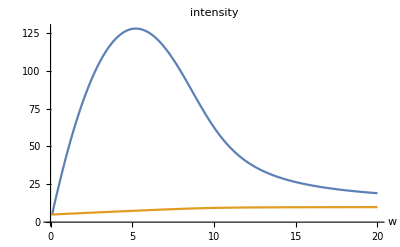

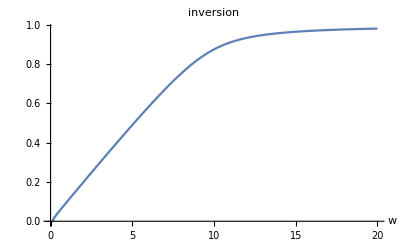

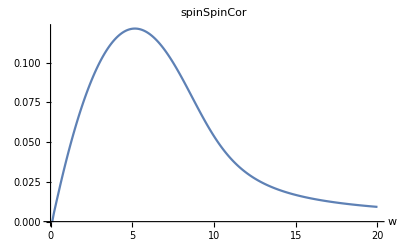

```mathematica
ListLinePlot[{intensityPlot,intensityUnCorPlot},PlotRange->All,PlotLabel->"intensity",AxesLabel->{"w"}]
ListLinePlot[inversionPlot,PlotRange->All,PlotLabel->"inversion",AxesLabel->{"w"}]
ListLinePlot[spinSpinCorPlot,PlotRange->All,PlotLabel->"spinSpinCor",AxesLabel->{"w"}]
```